-Graphics-
-Graphics-

(Bienvenidos a eScience - Estadistica!
https://github.com/josemramirez/mmaescience/statistics -[for Statistical M.])_beta^v14

# Statistical Mechanics - Lec. 2 I.D The Second Law

```mathematica
Thermodynamics: A Practical Journey to Abstract Concepts
```

The origins of thermodynamics can be traced back to the Industrial Revolution of the 19th century and the emergence of heat engines. This practical necessity of improving engine efficiency paved the way for the development of profound theoretical concepts. One such abstract idea that emerged from these pragmatic pursuits is the notion of entropy.

As engineers grappled with maximizing the performance of heat engines, they encountered fundamental principles that governed the behavior of energy and its transformations. These principles, initially derived from empirical observations and experimental findings, laid the foundation for the formulation of the laws of thermodynamics.

The first law of thermodynamics, which addresses the conservation of energy, established that energy cannot be created or destroyed but can only change form. This principle provided a quantitative framework for understanding the energy exchanges that occur during the operation of heat engines and other thermodynamic processes.

However, it was the second law of thermodynamics that introduced the revolutionary concept of entropy. This law dictated the inevitable dissipation of energy and the existence of an intrinsic disorder or randomness in nature. The concept of entropy quantified this disorder, offering insights into the directionality of natural processes and the limitations imposed on the efficiency of heat engines.

Through the lens of entropy, thermodynamics transcended its practical origins and unveiled profound implications for the fundamental nature of the universe. The concept of entropy has far-reaching consequences, influencing fields ranging from information theory to cosmology, and providing a unifying framework for understanding the arrow of time and the eventual fate of the universe.

Thus, what began as a quest to optimize the performance of practical devices evolved into a deep theoretical framework that not only revolutionized our understanding of energy and its transformations but also unveiled the inherent complexity and order underlying the natural world.

(2) -- An idealized heat engine operates by absorbing heat QH from a high-temperature reservoir (e.g., a coal fire), converting a fraction of it into useful work W, and rejecting the remaining heat QC to a low-temperature reservoir (e.g., the atmosphere). The efficiency η of the engine is determined by the ratio of the work output W to the heat input QH, expressed as:

η = W/QH

This fundamental relation encapsulates the essence of the second law of thermodynamics, which imposes a theoretical limit on the maximum efficiency attainable by any heat engine operating between two thermal reservoirs.

Statistical Mechanics
Ramirez (3)

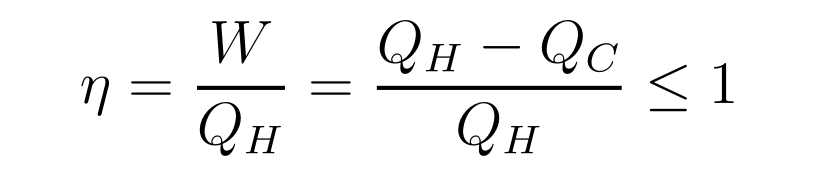

```mathematica
MaTeX["\\eta=\\frac{W}{Q_{H}}=\\frac{Q_{H}-Q_{C}}{Q_{H}} \\leq 1", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace["\\eta=\\frac{W}{Q_{H}}=\\frac{Q_{H}-Q_{C}}{Q_{H}} \\leq 1",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

η==W/Q_H==(Q_H-Q_C)/Q_H≤1

```mathematica
(4) -- An idealized refrigerator operates in a manner analogous to an engine running in reverse, utilizing work W to extract heat QC from a cold system and expelling heat QH at a higher temperature. This cyclic process can be characterized by a figure of merit, known as the coefficient of performance (COP), which quantifies the refrigerator's efficiency in transferring heat from the cold reservoir to the hot reservoir. The COP is defined as the ratio of the heat extracted from the cold reservoir to the work input required for the refrigeration cycle:

COP = QC / W

For an ideal, reversible refrigeration cycle operating between temperatures TC (cold reservoir) and TH (hot reservoir), the maximum achievable COP is given by the Carnot limit:

COP_Carnot = TC / (TH - TC)

This expression highlights the fundamental trade-off between the COP and the temperature span across which the refrigerator operates, with a larger temperature difference leading to a lower maximum COP.
```

Statistical Mechanics
Ramirez (5)

```mathematica
MaTeX["\\omega=\\frac{Q_{C}}{W}=\\frac{Q_{C}}{Q_{H}-Q_{C}}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\omega=\\frac{Q_{C}}{W}=\\frac{Q_{C}}{Q_{H}-Q_{C}}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ω==Q_C/W==Q_C/(Q_H-Q_C)

(6) -- The first law prohibits the existence of 'perpetual motion machines of the first kind', devices that generate work without consuming any energy. However, the conservation of energy principle permits engines that produce work by converting water to ice. Such a 'perpetual motion machine of the second kind' would solve global energy challenges, but it is forbidden by the second law of thermodynamics. The natural direction of heat flow from hotter to colder bodies constitutes the essence of the second law. There are several formulations of the second law, including the following two statements:

1. The entropy (S) of an isolated system not in equilibrium will tend to increase over time, approaching a maximum value at equilibrium.
    ΔS ≥ 0

2. No process is possible whose sole result is the transfer of heat from a cooler to a hotter body.

These statements encapsulate the unidirectional nature of spontaneous processes and the dissipation of energy in the form of heat, precluding the existence of perpetual motion machines of the second kind.

```mathematica
(7) -- Kelvin's statement asserts the impossibility of a process solely converting heat into work. This fundamental principle, also known as the Second Law of Thermodynamics, imposes a unidirectional constraint on the spontaneous flow of heat and the attainable efficiency of heat engines. 

It states: "No process is possible whose sole result is the complete conversion of heat into work."

In essence, this law dictates that a certain amount of energy must be dissipated as heat, rendering the complete conversion of heat into work an unattainable feat. This dissipation, often referred to as entropy production, is an inevitable consequence of irreversible processes occurring in nature.
```

(8) -- Heat cannot spontaneously flow from a colder to a hotter body. This fundamental principle, known as Clausius's Statement, is a cornerstone of thermodynamics. It asserts the impossibility of a process where the sole outcome is the transfer of thermal energy from a lower-temperature reservoir to a higher-temperature one without any additional driving force or external work being performed on the system.

(10) -- A perfect engine is ruled out by the first statement, a perfect refrigerator by the second. In fact the two statements are equivalent as shown below.

(11) -- The equivalence of the Kelvin and Clausius statements is established by demonstrating that the violation of one statement implies the violation of the other. Consider a hypothetical process that violates the Kelvin statement, which states that it is impossible to construct a cyclically operating device that produces no other effect than the absorption of heat from a single reservoir and the performance of an equal amount of work. If such a process were possible, it could be employed to transfer heat from a colder to a hotter body without the expenditure of work, thereby violating the Clausius statement, which asserts the impossibility of transferring heat from a colder to a hotter body without the intervention of an external agency.

Conversely, suppose a process exists that violates the Clausius statement, allowing heat to spontaneously flow from a colder to a hotter body without the aid of an external agency. By operating this process in reverse, it would be feasible to construct a cyclically operating device that absorbs heat from a single reservoir and performs an equal amount of work, thus violating the Kelvin statement.

Therefore, the Kelvin and Clausius statements are equivalent formulations of the second law of thermodynamics, as the violation of one statement necessitates the violation of the other.

(12) -- In the realm of thermodynamics and statistical mechanics, the principles of Clausius and Kelvin serve as cornerstones, safeguarding the fundamental laws that govern the behavior of energy and its transformations. Let us delve into the profound implications of these principles.

(a) Imagine a hypothetical machine that defies Clausius's statement by transferring heat Q from a cooler temperature TC to a higher temperature TH. Now, consider an engine operating between these two temperatures, absorbing heat QH from TH and rejecting QC at TC. The combined system would extract QH - Q from TH, produce work equal to QH - QC, and dissipate QC - Q at TC. If we adjust the engine's output such that QC = Q, the net result would be a 100% efficient engine, violating Kelvin's statement.

(b) Alternatively, let us postulate a machine that contravenes Kelvin's law by converting heat Q entirely into work. The work output of this machine could then be utilized to power a refrigerator, resulting in the transfer of heat from a colder to a hotter body, thus violating Clausius's statement.

The intrinsic contradiction inherent in these hypothetical scenarios underscores the profound truth enshrined within the principles of Clausius and Kelvin. They serve as inviolable pillars, ensuring the integrity of thermodynamics and safeguarding the fundamental laws that govern the universe's energy transformations.

```mathematica
(13) -- Although these statements may appear as rather trivial and qualitative descriptions, they have important quantitative implications as demonstrated in the next sections.
```

```mathematica
I.E Carnot Engines & Thermodynamic Temperature
```

A Carnot Engine is a theoretical construct that operates in a reversible cycle, where heat is absorbed from a high - temperature reservoir (source) at temperature T_H and rejected to a low - temperature reservoir (sink) at temperature T_C . The efficiency of a Carnot Engine represents the maximum attainable efficiency for any heat engine operating between these two temperature reservoirs . This efficiency is solely determined by the temperatures T_H and T_C, independent of the working substance or the details of the cycle .

```mathematica
(15) -- A reversible process is one that can be run backward in time by simply reversing its inputs and outputs. It is the thermodynamic equivalent of frictionless motion in mechanics. Since time reversibility implies equilibrium, a reversible transformation must be quasistatic, but the reverse is not necessarily true (e.g., if there is energy dissipation due to friction). An engine that runs in a cycle returns to its original internal state at the end of the process. The distinguishing characteristic of the Carnot engine is that heat exchanges with the surroundings are carried out only at two temperatures. The zeroth law allows us to select two isotherms at temperatures $T_{H}$ and $T_{C}$ for these heat exchanges. To complete the Carnot cycle we have to connect these isotherms by reversible adiabatic paths in the coordinate space. Since heat is not a function of state, we don't know how to construct such paths in general. Fortunately, we have sufficient information at this point to construct a Carnot engine using an ideal gas as its internal working substance. For the purpose of demonstration, let us compute the adiabatic curves for a monatomic ideal gas with an internal energy
```

Statistical Mechanics
Ramirez (16)

```mathematica
MaTeX["E=\\frac{3}{2} N k_{B} T=\\frac{3}{2} P V", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["E=\\frac{3}{2} N k_{B} T=\\frac{3}{2} P V",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ⅇ==3/2 N k_B T==(3 P V)/2

(17) -- Along a quasi-static path, the entropy change of a system is given by the integral:

∫(δQ/T)

This integral represents the sum of the infinitesimal heat transfers, δQ, divided by the absolute temperature, T, at which each transfer occurs. The entropy change is a state function, meaning it depends solely on the initial and final states, not the specific path taken between them.

For a reversible process, the equality holds:

∫(δQ/T) = ΔS

Where ΔS is the change in entropy between the initial and final states.

However, for an irreversible process, the inequality applies:

∫(δQ/T) < ΔS

This inequality arises due to the generation of entropy during irreversible processes, such as friction, dissipation, or other non-quasi-static effects.

Statistical Mechanics
Ramirez (18)

```mathematica
MaTeX["d Q=d E-d W=d\\left(\\frac{3}{2} P V\\right)+P d V=\\frac{5}{2} P d V+\\frac{3}{2} V d P", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d Q=d E-d W=d\\left(\\frac{3}{2} P V\\right)+P d V=\\frac{5}{2} P d V+\\frac{3}{2} V d P",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

dQ==dE-dW==d[(3 P V)/2]+PdV==(5 P d V)/2+(3 V d P)/2

(19) -- The adiabatic condition, dQ = 0, signifies a process in which no heat is exchanged between the system and its surroundings. This constraint imposes a specific path that the system must follow in its thermodynamic evolution. The adiabatic process represents a special case where the system's internal energy remains constant, as no external work is performed or received. Consequently, the system's temperature, pressure, and volume may change, but the total energy remains unaltered, governed by the first law of thermodynamics. This condition is particularly relevant in various applications, including the study of heat engines, refrigeration cycles, and certain idealized models in statistical mechanics.

Statistical Mechanics
Ramirez (20)

```mathematica
MaTeX["\\frac{d P}{P}+\\frac{5}{3} \\frac{d V}{V}=0, \\Longrightarrow P V^{\\gamma}=\\text {constant}", Magnification -> 4]
```

-Graphics-

```mathematica
(21) -- With γ = 5/3, the adiabatic curves are clearly distinct from the isotherms. We can select two such adiabatic curves to intersect our isotherms, thereby completing a Carnot cycle. The assumption of E ∝ T is not necessary, and in the test 1 review problems, you will construct adiabatics for any E(T) functional form. In fact, a similar construction is possible for any two-parameter system with E(J, x), where J and x represent the extensive variables of the system.

The adiabatic curves, representing processes without heat exchange, are distinct from the isotherms, which represent processes at constant temperature. By selecting two adiabatic curves that intersect the isotherms, we can construct a Carnot cycle, a fundamental concept in thermodynamics. The energy dependence on temperature, E(T), need not be linear, and you will explore various functional forms in the review problems. Moreover, this construction extends to systems described by two extensive variables, J and x, where the energy depends on both variables, E(J, x).
```

Carnot's Theorem

states the fundamental limit on the efficiency of any heat engine operating between two thermal reservoirs at temperatures TH (hotter) and TC (colder). No engine can surpass the efficiency of a reversible Carnot cycle operating between the same temperature limits. This principle arises from the Second Law of Thermodynamics and forms the cornerstone of classical thermodynamics, establishing the absolute scale of temperature and the unattainability of a perpetual motion machine of the second kind.

```mathematica
(23) -- The reversibility of a Carnot engine allows it to operate as a refrigerator when driven in reverse. Consider a non-Carnot engine driving a Carnot engine backward. Let $Q_H, Q_C$ and $Q_H', Q_C'$ denote the heat exchanges of the non-Carnot and Carnot engines, respectively. The net effect is to transfer heat equal to $Q_H - Q_H' = Q_C - Q_C'$ from $T_H$ to $T_C$. Clausius's statement dictates that the quantity of transferred heat cannot be negative, i.e., $Q_H \geq Q_H'$. Since the same amount of work $W$ is involved in this process, we conclude that the efficiency of the Carnot engine exceeds that of the non-Carnot engine for the same temperature limits.
```

Statistical Mechanics
Ramirez (24)

```mathematica
MaTeX["\\frac{W}{Q_{H}} \\leq \\frac{W}{Q_{H}^{\\prime}}, \\quad \\Longrightarrow \\quad \\eta_{\\text {Carnot}} \\geq \\eta_{\\text {non-Carnot}}", Magnification -> 4]
```

-Graphics-

```mathematica
(25) -- The efficiency of a reversible (Carnot) engine is determined solely by the temperature of the hot reservoir (TH) and the cold reservoir (TC). It is independent of the working substance or the specific design of the engine. This universal efficiency, η(TH, TC), is the maximum possible efficiency for any heat engine operating between these two temperature reservoirs. Any reversible engine can be used to drive another reversible engine in reverse, with the same efficiency but in the opposite direction. This reciprocal relationship validates the universality of the Carnot efficiency for all reversible processes.
```

(26) -- The maximum efficiency of a Carnot engine is solely dependent on the temperatures of the hot and cold reservoirs, regardless of the working substance or the engine's design and construction. This remarkable property allows us to establish a temperature scale based on the performance of these ideal engines.

To construct such a scale, we first explore how the efficiency η(TH, TC) depends on the two temperatures. Consider two Carnot engines operating in series, one between temperatures T1 and T2, and the other between T2 and T3 (T1 > T2 > T3). Let Q1, Q2, W12 represent the heat exchanges and work output of the first engine, and Q2, Q3, W23 for the second engine. Since the heat rejected by the first engine is absorbed by the second, their combined effect is equivalent to another Carnot engine with heat exchanges Q1, Q3, and work output W13 = W12 + W23. The three heats are related by:

Q1 - Q3 = W13

Substituting the expressions for the work outputs, we obtain:

Q1 - Q3 = Q1(1 - T2/T1) + Q2(1 - T3/T2)

Rearranging and using the fact that Q2 = Q1 - Q3, we find:

Q3/Q1 = (T3/T2) / (T1/T2)

Thus, the ratio of heat exchanges in a Carnot cycle depends only on the temperature ratios, independent of the working substance.

Statistical Mechanics
Ramirez (27)

```mathematica
MaTeX["Q_{2}=Q_{1}-W_{12}=Q_{1}\\left[1-\\eta\\left(T_{1}, T_{2}\\right)\\right]", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["Q_{2}=Q_{1}-W_{12}=Q_{1}\\left[1-\\eta\\left(T_{1}, T_{2}\\right)\\right]",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

Q_2==Q_1-W_12==Q_1[1-η[T_1,T_2]]

Statistical Mechanics
Ramirez (28)

```mathematica
MaTeX["\\begin{gathered}Q_{3}=Q_{2}-W_{23}=Q_{2}\\left[1-\\eta\\left(T_{2}, T_{3}\\right)\\right]=Q_{1}\\left[1-\\eta\\left(T_{1}, T_{2}\\right)\\right]\\left[1-\\eta\\left(T_{2}, T_{3}\\right)\\right] \\\\Q_{3}=Q_{1}-W_{13}=Q_{2}\\left[1-\\eta\\left(T_{1}, T_{3}\\right)\\right]\\end{gathered}", Magnification -> 4]
```

-Graphics-

```mathematica
(29) -- Comparison of the final two expressions yields
```

Statistical Mechanics
Ramirez (30)

```mathematica
MaTeX["\\left[1-\\eta\\left(T_{1}, T_{3}\\right)\\right]=\\left[1-\\eta\\left(T_{1}, T_{2}\\right)\\right]\\left[1-\\eta\\left(T_{2}, T_{3}\\right)\\right]", Magnification -> 4]
```

-Graphics-

```mathematica
(31) -- The property of the Carnot efficiency, η(T₁, T₂), implies that 1 - η(T₁, T₂) can be expressed as a ratio of the form f(T₂) / f(T₁). By convention, this ratio is set to T₂ / T₁, where T₁ and T₂ are the absolute temperatures of the heat reservoirs between which the Carnot engine operates. This convention arises from the fundamental principles of thermodynamics and the statistical behavior of microscopic systems.
```

Statistical Mechanics
Ramirez (32)

```mathematica
MaTeX["\\begin{aligned}1-\\eta\\left(T_{1}, T_{2}\\right) & =\\frac{Q_{2}}{Q_{1}} \\equiv \\frac{T_{2}}{T_{1}} \\\\\\Longrightarrow \\eta\\left(T_{H}, T_{C}\\right) & =\\frac{T_{H}-T_{C}}{T_{H}}\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
(33) -- The equation (I.22) defines temperature up to a constant of proportionality, which is set by choosing the triple point of water, ice, and steam at 273.16°K. Throughout this chapter, the symbols Θ and T have been used interchangeably. By running a Carnot cycle for a perfect gas, it can be proved (see text review problems) that the ideal gas and thermodynamic temperature scales are equivalent. 

The thermodynamic scale is conceptually advantageous as it is independent of the properties of any substance, although it is not practically useful. All thermodynamic temperatures are positive since, according to eq.(I.22), the heat extracted from a temperature T is proportional to it. If a negative temperature existed, an engine operating between it and a positive temperature would extract heat from both reservoirs and convert the sum total to work, violating Kelvin's statement of the second law.
```

I.F Entropy

The second law of thermodynamics provides a framework for constructing a new state function, known as entropy. This function serves as a quantitative measure of disorder or randomness within a system. The theorem states that for any reversible process occurring between equilibrium states, the integral of (δQ/T) evaluated along the path is independent of the specific path taken, provided the initial and final states remain fixed. Here, δQ represents the infinitesimal amount of heat transferred, and T is the absolute temperature at which the transfer occurs.

Symbolically, we express this as:

∫(δQ/T) = 0 (for a cyclic process)

This remarkable property allows us to define a new state function, entropy (S), such that its change between any two equilibrium states is given by:

ΔS = ∫(δQ/T) (for a reversible process)

Entropy plays a crucial role in determining the spontaneity and direction of natural processes. It quantifies the extent to which energy is dispersed or concentrated within a system, providing insights into the system's order and the availability of its energy to perform useful work.

Clausius's Theorem

posits an inequality for cyclic transformations, encompassing both reversible and irreversible processes. It states that for any closed cycle, the integral of the infinitesimal heat transfer divided by the absolute temperature, evaluated over the entire cycle, is less than or equal to zero: ∮(dQ/T) ≤ 0. Here, dQ represents the differential heat increment absorbed by the system at temperature T. This inequality establishes a fundamental constraint on the feasibility of cyclic processes, with the equality holding true exclusively for reversible cycles. Irreversible cycles, characterized by dissipative effects such as friction or inelastic deformations, necessarily result in a strict inequality, reflecting the inherent irreversibility and the associated degradation of energy quality.

```mathematica
(36) -- The proof involves subdividing the cycle into a series of infinitesimal transformations, where the system receives energy in the form of heat dQ and work dW. The system need not be in equilibrium at each interval. We direct all the heat exchanges of the system to one port of a Carnot engine, which has another reservoir at a fixed temperature T₀. Since the sign of dQ is not specified, the Carnot engine must operate a series of infinitesimal cycles in either direction. To deliver heat dQ to the system at some stage, the engine has to extract heat dQᵣ from the fixed reservoir. If the heat is delivered to a part of the system which is locally at a temperature T, then according to the equation (I.22), dQᵣ/dQ = T₀/T.
```

Statistical Mechanics
Ramirez (37)

```mathematica
MaTeX["d Q_{R}=T_{0} \\frac{d Q}{T}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d Q_{R}=T_{0} \\frac{d Q}{T}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

d Q_R==(T_0 dQ)/T

(38) -- In a thermodynamic cycle involving a Carnot engine and a system, the net effect is the extraction of heat QR = ∮dQR from the reservoir and its conversion into external work W. The work W = QR represents the sum of the work elements performed by the Carnot engine and the system throughout the complete cycle. According to Kelvin's statement of the second law, QR = W ≤ 0, indicating that the heat extracted from the reservoir is either equal to or less than the work done during the cycle.

Statistical Mechanics
Ramirez (39)

```mathematica
MaTeX["T_{0} \\oint \\frac{d Q}{T} \\leq 0, \\quad \\Longrightarrow \\quad \\frac{d Q}{T} \\leq 0", Magnification -> 4]
```

-Graphics-

(40) -- Since the temperature T₀ is greater than zero, it is important to note that the temperature T in equation (I.24) refers to the temperature of the entire system only for quasi-static processes, where it can be uniquely defined throughout the cycle. In cases other than quasi-static processes, T represents a local temperature, say at a boundary of the system, at which the Carnot engine deposits the element of heat.

```mathematica
Consequences of Clausius's theorem:
```

(42) -- For a reversible cycle, the contour integral of the heat exchanged in a reversible process divided by the absolute temperature, ∮(dQrev/T), is equal to zero. This result arises from the fact that upon reversing the direction of the cycle, the infinitesimal heat exchange reverses sign, dQrev → -dQrev, while the absolute temperature remains unchanged. Consequently, by the theorem stating that dQrev/T is simultaneously non-negative and non-positive for a reversible process, it must be identically zero.

This result has a profound implication: the integral of dQrev/T between any two points A and B is independent of the path taken, since for two distinct paths (1) and (2) connecting A and B, the contour integral ∮(dQrev/T) = 0. Therefore, the integral ∫A→B(dQrev/T) is solely determined by the end states A and B, and not by the specific trajectory followed between them.

Statistical Mechanics
Ramirez (43)

```mathematica
MaTeX["\\int _{A}^{B} \\frac{d Q_{\\mathrm{rev}}^{(1)}}{T_{1}}+\\int _{B}^{A} \\frac{d Q_{\\mathrm{rev}}^{(2)}}{T_{2}}=0, \\Longrightarrow \\int _{A}^{B} \\frac{d Q_{\\mathrm{rev}}^{(1)}}{T_{1}}=\\int _{A}^{B} \\frac{d Q_{\\mathrm{rev}}^{(2)}}{T_{2}}", Magnification -> 4]
```

-Graphics-

(44) -- The entropy S is a state function that can be derived from the fundamental relation (I.25). As the integral in (I.25) is path-independent and solely determined by the initial and final states, we can define the change in entropy ΔS between two equilibrium states 1 and 2 as:

ΔS = S2 - S1 = ∫(2,1) (δQ/T)

where δQ represents an infinitesimal amount of heat transfer, and T is the absolute temperature at which the transfer occurs. This definition ensures that the entropy is a well-defined state function, reflecting the irreversible nature of processes in isolated systems.

Statistical Mechanics
Ramirez (45)

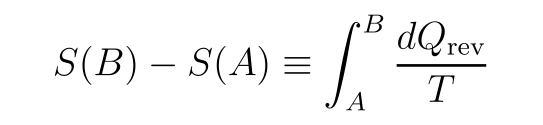

```mathematica
MaTeX["S(B)-S(A) \\equiv \\int _{A}^{B} \\frac{d Q_{\\mathrm{rev}}}{T}", Magnification -> 4]
```

```mathematica
(46) -- For reversible processes, the heat transfer dQ_rev can be computed using the fundamental relation dQ_rev = T dS. This equation enables us to construct adiabatic curves for a general (multi-variable) system by imposing the condition of constant entropy S. It is important to note that the equation (I.26) defines the entropy only up to an additive constant, which can be determined by imposing appropriate boundary conditions or by using the third law of thermodynamics.
```

(47) -- (3) Consider an irreversible change from $A$ to $B$. Make a complete cycle by returning from $B$ to $A$ along a reversible path.

Statistical Mechanics
Ramirez (48)

```mathematica
MaTeX["\\int _{A}^{B} \\frac{d Q}{T}+\\int _{B}^{A} \\frac{d Q_{\\mathrm{rev}}}{T} \\leq 0, \\quad \\Longrightarrow \\quad \\int _{A}^{B} \\frac{d Q}{T} \\leq S(B)-S(A)", Magnification -> 4]
```

-Graphics-

```mathematica
(49) -- In differential form, the second law of thermodynamics states that dS ≥ dQ/T for any transformation, where S is the entropy, Q is the heat transfer, and T is the absolute temperature. Consider an adiabatic system comprising multiple subsystems, each initially in equilibrium. As these subsystems interact and reach a state of joint equilibrium, the net heat transfer is zero, dQ = 0. Consequently, the entropy change δS must be greater than or equal to zero, δS ≥ 0. This implies that an adiabatic system attains its maximum entropy value at equilibrium, as spontaneous internal changes can only increase the entropy. The direction of increasing entropy thus defines the arrow of time and the path towards equilibrium.
```

(50) -- (4) For a reversible (hence quasi-static) transformation, $d Q=T d S$ and $d W=\sum_{i} J_{i} d x_{i}$, and the first law implies

Statistical Mechanics
Ramirez (51)

```mathematica
MaTeX["d E=d Q+d W=T d S+\\sum_{i} J_{i} d x_{i}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d E=d Q+d W=T d S+\\sum_{i} J_{i} d x_{i}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

dE==dQ+dW==TdS+∑_i J_i d x_i

(52) -- Equation (I.28) is a fundamental identity in thermodynamics, applicable to any process, reversible or irreversible. This equation expresses a profound relationship between entropy (S) and temperature (T), treating them as conjugate variables. Entropy assumes the role of a displacement, while temperature acts as the corresponding force. This conjugate relationship lies at the heart of thermodynamic processes and forms the basis for understanding the intricate interplay between energy and disorder in physical systems.

```mathematica
(53) -- (5) The number of independent variables necessary to describe a thermodynamic system also follows from eq.(I.28). If there are $n$ methods of doing work on a system, represented by $n$ conjugate pairs $\left(J_{i}, x_{i}\right)$, then $n+1$ independent coordinates are necessary to describe the system. (We shall ignore possible constraints between the mechanical coordinates.) For example, choosing $\left(E,\left\{x_{i}\right\}\right)$ as coordinates, it follows from eq.(I.28) that
```

Statistical Mechanics
Ramirez (54)

```mathematica
MaTeX["\\left.\\frac{\\partial S}{\\partial E}\\right|_{\\mathbf{x}}=\\frac{1}{T}, \\quad \\text {and}\\left.\\quad \\frac{\\partial S}{\\partial x_{i}}\\right|_{E, x_{j \\neq i}}=-\\frac{J_{i}}{T}", Magnification -> 4]
```

-Graphics-

(55) -- ( $\mathbf{x}$ and $\mathbf{J}$ will be used as short-hand notations for the parameter sets $\left\{x_{i}\right\}$ and $\left\{J_{i}\right\}$.)

```mathematica
mathPiXDB1="VarsPaper23_v1.mx";
DumpSave[$WorkDir<>"mathPiXDB/"<>mathPiXDB1,"Global`"];
```

◀ prev - + prox ▶

e Guardar
d Resetear